# Snapchat Filters

## Shannon Brownlee Adv. Topics 2019

## How can we use image processing in Mathematica to apply a filter based on changing facial features?

CurrentImage

The CurrentImage function takes a picture of whatever is visible from your computer’s webcam. Make sure Mathematica has permission to access the camera and that the camera is not turned off.

```mathematica
CurrentImage[]
```

FindFaces

Mathematica has a built-in function to identify faces in pictures. You can google any stock photo and use the function to identify the faces.

```mathematica
FindFaces[-Graphics-]
```

{Rectangle[{37.5,127.5},{72.5,162.5}],Rectangle[{88.5,109.5},{120.5,141.5}],Rectangle[{149.5,124.5},{182.5,157.5}],Rectangle[{207.5,123.5},{244.5,160.5}]}

Notice how the output is in the form of rectangles. These rectangles bound each of the faces in the image. 
But how can we visualize this?

HighlightImage

The function HighlightImage does exactly what the name implies -- it highlights a specified part of an image.

```mathematica
HighlightImage[-Graphics-,FindFaces[-Graphics-]]
```

-Graphics-

Now, what if instead of using a random stock image we used a picture of ourselves or the CurrentImage?

```mathematica
HighlightImage[CurrentImage[],FindFaces[CurrentImage[]]]
```

-Graphics-

We can edit the picture using different functions within HighlightImage, but that’s enough material for a different lesson.
Right now we want to focus on creating a filter that is generated based on certain facial features. For this, we need to know the dimensions and corner points of the rectangle bounding our face.

Bounding Rectangle

Recall that the output of just the function FindFaces[] is the bounding rectangle.

```mathematica
FindFaces[-Graphics-], Part
```

{Rectangle[{203.5,100.5},{463.5,360.5}]}

Now we have to figure out how to extract just the points of this list so that we can use them as points to add the graphics of our filter. To do this, we can use the functions Apply and List.

```mathematica
Apply[List,FindFaces[-Graphics-][[1]]]
```

{{203.5,100.5},{463.5,360.5}}

This gives us a list of the corners used to generate the bounding rectangle. Instead of further breaking this list down, we can simply assign variable names to each element inside the list.

```mathematica
{{a,b},{c,d}}=Apply[List,FindFaces[-Graphics-][[1]]]
```

{{203.5,100.5},{463.5,360.5}}

```mathematica
a
```

203.5

```mathematica
b
```

100.5

```mathematica
c
```

463.5

```mathematica
d
```

360.5

Now, each of these variables is equal to the x or y value of the bounding rectangle.

Graphics

In order to use these points, we need to figure out what shape(s) we’d like to put at the each space. For this example, we’re going to use a simple mouse ears filter.
Recall from Graphics:



```mathematica
Graphics[Disk[]]
```

We can spruce this up a little bit with some added options.

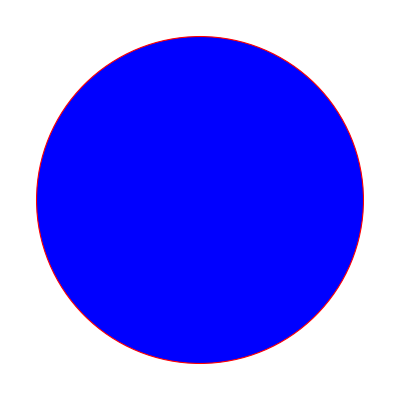

```mathematica
Graphics[{
Blue,EdgeForm[{Red,Thick,Dashed}],Disk[{0,0},10]}]
```

Remember: the options inside of Disk are Disk[{center point}, radius].

## Putting it all together

Let’s clean up our code a little bit by defining come variables. The semicolons after each line suppress the output.

```mathematica
img:=CurrentImage[];
```

```mathematica
faces:=FindFaces[img];
```

```mathematica
{{x1,y1},{x2,y2}}=Apply[List,faces[[1]]];
```

Now that these variables are set, let’s put it all together. The check function is just there to avoid getting a bunch of error messages in case something goes wrong. All it says is that if our code with HighlightImage doesn’t work, to output the CurrentImage.

```mathematica
Check[
HighlightImage[
img,
Graphics[
{{Blue,EdgeForm[{Red,Thick,Dashed}],Disk[{x1,y2+20},30]},{Blue,EdgeForm[{Red,Thick,Dashed}],Disk[{x2,y2+20},30]}}]],img]
```

-Graphics-

I added 20 to each of my y2 values since I noticed the ears tended to be placed a little too low on me! It all depends on what the FindFaces function detects to be the rectangle on your picture.

### And there you have it! A very basic Snapchat filter built using Mathematica!

## Further Experimentation

#### Feel free to try any other graphics you have in mind and fiddle with your point values. Have fun with it! I added a nose into my original code. :-P

```mathematica
img:=CurrentImage[];
faces=FindFaces[img];
{{x,y},{s,m}}=Apply[List,faces[[1]]];
Check[
HighlightImage[
img,
Graphics[
{{Blue,EdgeForm[{Red,Thick,Dashed}],Disk[{x,m},30]},{Blue,EdgeForm[{Red,Thick,Dashed}],Disk[{s,m},30]},{Blue,EdgeForm[{Red,Thick,Dashed}],Disk[{s-0.5x,m/2},8]}}]],img]
```

-Graphics-

# Project Reflection Section

Select the cell bracket for the entire section below and copy/paste it into the end of your Mathematica notebook. Complete the questions in paragraphs there.

## Project Reflection

### Project Information

Please make sure your name(s) and project title are at the top of the Mathematica notebook in their own cells appropriately styled.

Project Category:  Interdisciplinary/Mathematica Functionality

Project Type:  Computational Essay/Lesson

Date of Completion:  4/9/19

### Work and Organization

Please make sure you include a text cell with a project description at the top of your notebook.

Answer Here - If this is a group project, how was the work divided among group members?: 
 Rather than making this a group project, I focused on this lesson to get the final project, while Emily made her own related notebook which looked at HighlightImage in more depth.

### Project Goals

Did you meet your goals with this project?  
With this project, I met my goals of writing a lesson for CT@TP to create a photo filter. The final product isn’t dynamic, as initially, envisioned, but it reached all of the afore set goals.

How did the project change once you started?
This project was initially going to be completely based off of the code from a 2016 One-Liner, but that code didn’t seem to work on any of the computers I tried it on. It took much more work than initially expected since I had to basically build this from scratch.

What are the strengths and weaknesses of this project?  
This project is easy and fun and allows for some basic image processing along with exploring one of the built-in machine learning functions that Mathematica has. While the code works, it does not do so with complete accuracy. The FindFaces function is not incredibly accurate and kind of does its own thing, so each user has to fiddle around with the rest of the code. The final product is not dynamic as initially hoped, but maybe I can work on figuring out the issues with that.

Did you share your work with someone or a client? If so, what was the response?  
My fellow Advanced Topics students were very impressed with the final result and enjoyed playing around with the code.

### Learning

How did you learn by doing this project?  
I learned a lot more about notation in the Wolfram Language while working on this project (@@ for Apply, etc.), and I gained much more experience in image processing since I didn’t do the first Images assignment. I also worked with the DOcumentation Center a lot more since I had to build this from scratch and find similar functions to the ones I was using.

What would you do differently if you were to do this project again?  
If I were to do this project again, I would work more on making the project dynamic from the beginning instead of trying to figure it out with just a still picture. I would also consider creating my own facial identification neural net in order to possibly improve the accuracy of the code.

### Mathematics

How did you use mathematics in this project?  
I used math to generate points, as well as to design the graphics used.

### Peer Review

What did your reviewer like about your project? 
My reviewer liked the project’s topic, creativity, and originality.

What was your response to peer review? How did the project change because of review and/or what suggestions did you not take?  
I expected what my peer reviewer had said about my project, and so I made the graphics section a little longer and more interesting.

### Additional Information

Other thoughts, comments, ideas, etc.?

## Credits

This project was inspired by and loosely based upon Philip Maymin’s “Mickey Mousical” from the 2016 Wolfram One-Liner Competition. It can be found here.